# Spectral Lags in Very High Energy Emission of Gamma Ray Bursts

## Model

Relativity

```mathematica
v[γ_]:=√(1-1/γ^2);
```

Cosmology

```mathematica
ΩΛ[Ωm_]:=1-Ωm;
```

```mathematica
universe={Hobs_,Ωm_};
```

```mathematica
distance[universe,z_]:=1/Hobs √(1/ΩΛ[Ωm])((1+z)Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm](1+z)^3]-Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm]]);
```

```mathematica
photonSphereArea[universe_,z_]:=4π distance[universe,z]^2;
```

```mathematica
burstsSphereArea[universe_,z_]:=(4π distance[universe,z]^2)/(1+z)^2;
```

```mathematica
shellVolumePerRedshift[universe,z_]:=(4π distance[{Hobs,Ωm},z]^2)/(1+z)^3 1/(Hobs √(Ωm(1+z)^3+ΩΛ[Ωm]));
```

Burst

```mathematica
burst={γ_,η0_,r0_,n_,ω0_,θ0_,k_,α_};
```

Observer

```mathematica
observer={detectorArea_,z_,χ_};
```

Light curve

```mathematica
i[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
1/(2k)ω(ω/ω0)^α ExpIntegralE[(α+1)/(2k)+1,(θ/θ0)^2(ω/ω0)^(-2k)(v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2k)]
];
```

```mathematica
j[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z))^3 π/(n Sin[(3π)/n]),
τ^3/3 Hypergeometric2F1[1,3/n,(n+3)/n,-(τ/(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z)))^n]
];
```

```mathematica
p[universe_,burst,observer,{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,χ,∞},{ϕ,0,π}])
];
```

Duration

```mathematica
Options[duration]={part->0.99};
```

```mathematica
duration[universe_,burst,observer,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,observerValues,p∞,precision},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
observerValues={detectorArea,z,χ};
p∞=p[universe,burstValues,observerValues,{0.,∞},{ω1,ω2}];
pi[τ_?NumberQ]:=p[universe,burstValues,observerValues,{0.,τ},{ω1,ω2}];
τ/.FindRoot[pi[τ]-OptionValue[part]p∞,{τ,r0/γ^2(1.+z)}]
];
```

Stretching factor

```mathematica
jτ[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
0,
τ^2/(1+((2τ)/(r0 (1+z) (-2+2/v[γ]+θ^2+χ^2-2 θ χ Cos[ϕ])))^n)
];
```

```mathematica
pτ[universe_,burst,observer,τ_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,χ,∞},{ϕ,0,π}])
];
```

```mathematica
Options[κ]={δ->0.01,accurateQ->Automatic};
```

```mathematica
κ[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{p12∞,p23∞,diff,diffτ,δτ,τmiddle,τend,κmin,κmax,minDifference,maxDifference,diffDifference,precision,accQ},
p12∞=p[universe,burst,observer,{0.,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0.,∞},{ω2,ω3}];
diff[τ_?NumberQ,κ_?NumberQ]:=p[universe,burst,observer,{0.,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0.,κ τ},{ω2,ω3}]/(p23∞);
diffτ[τ_?NumberQ,κ_?NumberQ]:=pτ[universe,burst,observer,τ,{ω1,ω2}]/(p12∞)-κ pτ[universe,burst,observer,κ τ,{ω2,ω3}]/(p23∞);
accQ=OptionValue[accurateQ];
If[TrueQ[accQ],
τend=duration[universe,burst,observer,{ω1,ω3}];
δτ=OptionValue[δ]τend;
maxDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]>0,
If[diff[τend,κ]>0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,zero-δτ}];
];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
];
minDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]<0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
If[diff[τend,κ]<0,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,zero+δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
]
];
κmin=κ/.FindRoot[diff[δτ,κ],{κ,1.}];
κmax=κ/.FindRoot[diff[τend,κ],{κ,1.}];
diffDifference[κ_?NumberQ]:=maxDifference[κ][[2]]+minDifference[κ][[2]];
κ/.FindRoot[diffDifference[κ],{κ,κmin,κmax}]
,
τmiddle=duration[universe,burst,observer,{ω1,ω3},part->0.5];
κ/.FindRoot[diff[τmiddle,κ],{κ,1.}]
]
];
```

Total Energy

```mathematica
energy[burst,ω1_]:=(16 π^3)/(3n(-2k-α-2)Sin[(3π)/n])γ^(-2k-α)(1-1/(4 γ^2))η0 r0^3 θ0^2 ω0^(-2k-α)/ω1^(-2k-α-2);
```

Spectrum

```mathematica
iω[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
Exp[-(θ/θ0)^2 (ω/ω0)^(-2 k) (v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2 k)] (ω/ω0)^α
];
```

```mathematica
pω[universe_,burst,observer,{τ1_,τ2_},ω_]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))iω[burstValues,z,χ,ω,θ,ϕ](j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))iω[burstValues,z,χ,ω,θ,ϕ](j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,χ,∞},{ϕ,0,π}])
];
```

```mathematica
pω[defaultUniverse[],defaultBurst[γ->300],defaultObserver[χ->0.01],{0,∞},0.15]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

31824.9

```mathematica
pωe[universe_,burst_,observer_,{τ1_,τ2_},ω_]:=p[universe,burst,observer,{τ1,τ2},ω{1.,1.+1.*^-10}]/(ω 1.*^-10);
```

```mathematica
index[universe_,burst_,observer_,{ω1_,ω2_}]:=1/(Log[ω2]-Log[ω1])(Log[pωe[universe,burst,observer,{0.,∞},ω2]]-Log[pωe[universe,burst,observer,{0.,∞},ω1]]);
```

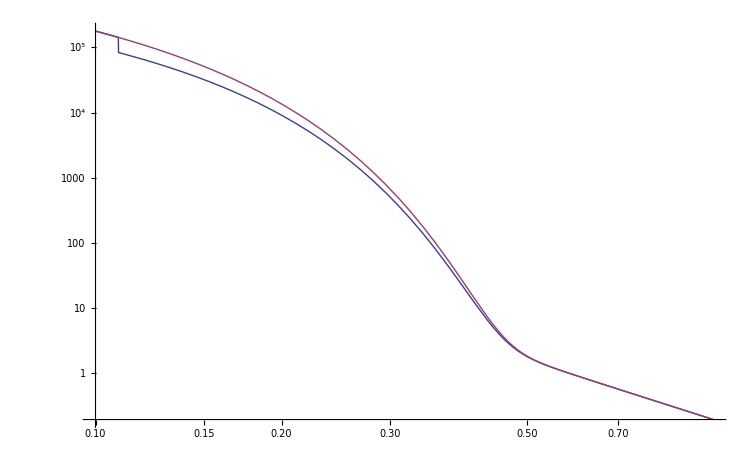

```mathematica
PrintTemporary[Dynamic[ω]];
int[ω_?NumberQ]:=pω[defaultUniverse[],defaultBurst[γ->300],defaultObserver[χ->0.01],{0,∞},ω];
inte[ω_?NumberQ]:=pωe[defaultUniverse[],defaultBurst[γ->300],defaultObserver[χ->0.01],{0,∞},ω];
LogLogPlot[{int[ω],inte[ω]},{ω,0.1,1},PlotRange->All]
```

Case Study

```mathematica
Options[defaultUniverse]={Hobs->2*^-18,Ωm->0.317};
```

```mathematica
defaultUniverse[OptionsPattern[]]:={OptionValue[Hobs],OptionValue[Ωm]};
```

```mathematica
Options[defaultBurst]={γ->100.,η0->1.*^45,r0->2.*^3,n->6,ω0->1.,θ0->5*^-6,k->-1,α->-1};
```

```mathematica
defaultBurst[OptionsPattern[]]:={OptionValue[γ],OptionValue[η0],OptionValue[r0],OptionValue[n],OptionValue[ω0],OptionValue[θ0],OptionValue[k],OptionValue[α]};
```

```mathematica
Options[defaultObserver]={detectorArea->5.563*^-18,z->1.,χ->0.};
```

```mathematica
defaultObserver[OptionsPattern[]]:={OptionValue[detectorArea],OptionValue[z],OptionValue[χ]};
```